```mathematica
1.NALOGA
```

```mathematica
ReplaceAll[x->{1,2,3,4}][(x^5-2x^2+3x+4)/(x^5-2x-1)]
```

{-3,34/27,119/118,144/145}

```mathematica
Table[(x^5-2x^2+3x+4)/(x^5-2x-1), {x, 1, 10}]
```

{-3,34/27,119/118,144/145,1547/1557,7726/7763,8367/8396,32668/32751,29459/29515,99834/99979}

```mathematica
2.NALOGA
```

```mathematica
Sez={10,20,30,40,50,60,70}
```

{10,20,30,40,50,60,70}

```mathematica
Sez[[{1,2,3}]]
```

{10,20,30}

```mathematica
Sez[[{-1,-2}]]
```

{70,60}

```mathematica
Sez[[{2,3,4}]]
```

{20,30,40}

```mathematica
Sez[[{2,3,5}]]
```

{20,30,50}

```mathematica
Drop[Sez, {4,5}]
```

{10,20,30,60,70}

```mathematica
3.NALOGA
```

```mathematica
Sez={x^6, x^2, a}
```

{x^6,x^2,a}

```mathematica
Sez/.{{x->3}, {x->x^2}, {x^2->x}, {x-> {1,2,3}}, {x->3,a->x}}
```

{{729,9,a},{x^12,x^4,a},{x^6,x,a},{{1,64,729},{1,4,9},a},{729,9,x}}

```mathematica
Sez//.{x->3, a->x}
```

{729,9,3}

```mathematica
4.NALOGA
```

```mathematica
ClearAll[x]
```

```mathematica
f[x_]:=x^5+4x^3-9
```

```mathematica
D[f[x],x]
```

12 x^2+5 x^4

```mathematica
D[f[x],x ]/. x->{1,5}
```

{17,3425}

```mathematica
f[x_]:=E^(x^(1/4))
```

```mathematica
D[f[x],x]/.x->{1,2}
```

{ⅇ/4,(ⅇ^(2^(1/4)))/(4 2^(3/4))}

```mathematica
f[x_]:=Abs[x+1]
```

```mathematica
FullSimplify[D[f[x],x], x∈Reals]
```

x^2 ((4 x)/(5+4 x)+3 Log[5+4 x])

```mathematica
f[x_]:=ax^2+3b
```

```mathematica
D[f[x],x]/.x->{1,2}
```

0

```mathematica
5.NALOGA
```

```mathematica
f[x_]:=x^3 Log[4x+5]
```

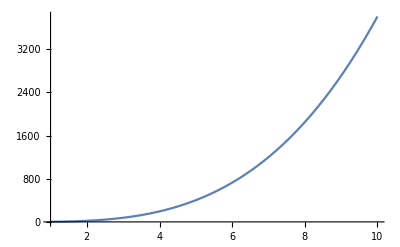

```mathematica
Plot[f[x],{x, 1, 10}]
```

```mathematica
n0=FullSimplify[f[x]/.x->5]
```

250 Log[5]

```mathematica
D[f[x],x]
```

(4 x^3)/(5+4 x)+3 x^2 Log[5+4 x]

```mathematica
k0=D[f[x],x]/. x->5
```

20+75 Log[25]

```mathematica
ClearAll[n0]
```

```mathematica
t[x_]:= k0 x+n0
```

```mathematica
D[t[x],x]
```

20+75 Log[25]

```mathematica
n0=FullSimplify[D[t[x],x]/.x->5]
```

20+75 Log[25]

```mathematica
20+75 Log[25]
```

```mathematica
t[x_]:= k0 x+n0
```

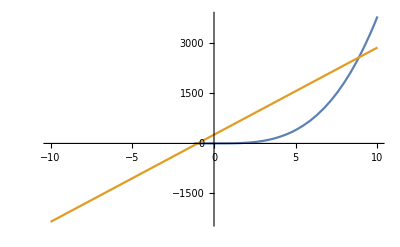

```mathematica
Plot[{f[x],t[x]}, {x, -10, 10}]
```

```mathematica
narisi[x0_]:=Module[{k0, n0, t},
k0= [f[x], x]/.x->x0;
n0=n/.First[Solve[f[x0]]]
```

```mathematica
6.NALOGA
```

```mathematica
Limit[(x^3-4x^2+2x+4)/(x^5-9x-14),x->2]
```

-2/71

```mathematica
Expand[(x^2−1)/(x^2−4)]
```